# Thermodynamics People Plot

Could not reproduce the code provided

GeoServer::vtiles: Unable to download one or more vector tiles.

Options::optnf: Method is not a known option for GeoGraphics.

ReplaceAll::reps: {Method} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FilterRules::rep: Method is not a valid replacement rule.

Join::heads: Heads List and FilterRules at positions 1 and 2 are expected to be the same.

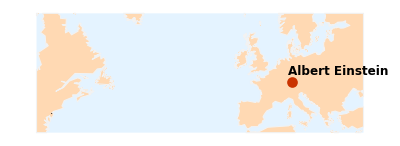

```mathematica
With[{people={}},Show[GeoListPlot[#["DeathPlace"]&/@people,PlotStyle->Black],GeoListPlot[Labeled[#["BirthPlace"],Style[#["Name"]/.{"Josiah Willard Gibbs"->"J. Willard Gibbs", "Lord Kelvin"->"Kelvin (William Thomson)"},12]]&/@people,PlotStyle->Red],
GeoGraphics[{Red,Dotted,Thickness[.005],GeoPath[{#["DeathPlace"],#["BirthPlace"]},
"Geodesic"
]&/@people
}],GeoBackground->{"Coastlines","Ocean"->Lighter[LightBlue,.2],"Land"->Lighter[Orange,.7],"Border"->Lighter[Gray,.9]},GeoProjection->"Mercator",GeoRange->{{35,62},{-80,35}}
]]
```